testList.txt

errorList.txt

-Graphics3D-

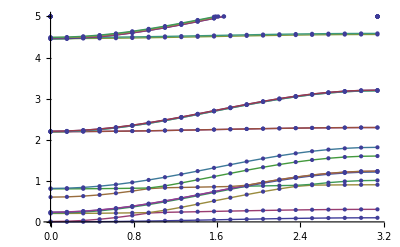

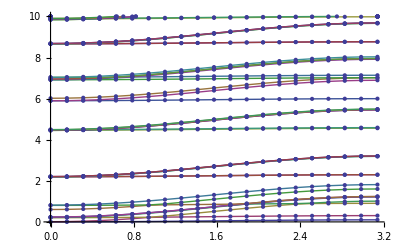

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Get["Methods.m",Path->FileNameJoin[{Directory[],"Packages"}]]

ϵ1=10;
ϵ2=5;
H=12;(*Height of first layer in angstroms*)
a= 3.904;(*unit cell size in angstroms*)
t1=.25;(*hopping parameters in eV*)
t2=.025;
MM=8;
NN=4;
β=.95;(*percent of the old distribution to keep when calculating the new distribution*)
numPartitions=20;
numStates=20;

SetParameters[ϵ1,ϵ2,H, a,  t1,t2, MM, NN, β, numPartitions, numStates];
Initialize[];
(*firstGuess=Flatten[Table[
	 1,
	{i,1,NN},
	{j,1,MM-1}
],1];
firstGuess=totalCharge/(firstGuess//Total)firstGuess;*)

firstGuess=2{0.00003674351315657139,0.007654011226030221,0.5124401953050349,1.2877654891450792,0.5124436831763184,0.007654314024021548,0.00003685191144502304,-5.765163617398043*^-7,4.837897254279863*^-6,0.000322506999056578,0.0009812573607791625,0.0003225137854577016,4.8564728552204246*^-6,-5.586994773048793*^-7,-2.709756164816698*^-7,-4.989874773312316*^-7,-5.730384827902701*^-7,-4.794641756990103*^-7,-5.730358435351914*^-7,-4.989775524442865*^-7,-2.709673000049558*^-7,-1.235496731920059*^-7,-2.282898420431577*^-7,-2.982672134049578*^-7,-3.2282941716190303*^-7,-2.982672130387085*^-7,-2.282898403750573*^-7,-1.2354967377967432*^-7};

{listvals,errorList}=SelfConsistentDistribution[firstGuess,.00005];
Export["testList.txt",listvals,"List"]
Export["errorList.txt",errorList,"List"]
PlotFullSpaceDistribution[listvals]
bandList=BandStructureList[listvals];
BandStructurePlot[0,5,bandList]
BandStructurePlot[0,10,bandList]
```

```mathematica
listvals//Total
totalCharge//Abs
```

2.33

4.54728

4.65932